# Notebook for : Geodesic equation in Schwarzschild-(anti-)de Sitter space-times: Analytical solutions and applications by Hackmann and Lammerzahl

Geoff Cope	
University of Utah
January 29,2021

```mathematica
(* See From Lagrangians to Hamiltonians Notebook *)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book And Review Article (Add Article)

```mathematica
Hyperlink["Geodesic equation in Schwarzschild-(anti-)de Sitter space-times:
Analytical solutions and applications by Hackmann and Lammerzahl",
"https://arxiv.org/abs/1505.07973"]
```

[Geodesic equation in Schwarzschild-(anti-)de Sitter space-times:
Analytical solutions and applications by Hackmann and Lammerzahl](https://arxiv.org/abs/1505.07973)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 779 Kb

{Utilities`CleanSlate`,XMPTools`Metadata`Domains`XMP`,XMPTools`Metadata`Domains`IPTC`,XMPTools`Metadata`Domains`Exif`,XMPTools`Wrappers`,XMPTools`Helpers`,DocumentationTools`GuidePages`,GeneralRelativityTensors`,VariationalMethods`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[
metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 4 dS adS

```mathematica
Clear[mReplace]
mReplace = 
M == Subscript[r,s]/2
```

M==r_s/2

```mathematica
(* We leave this in terms of M just for readability - will replace at bottom *) 

Clear[eq4]
eq4 = 
( 1 - (2 M)/r- (Λ/3)r^2) dt^2- ( 1 - (2 M)/r- (Λ/3)r^2)^-1 dr^2 - r^2 ( dθ^2 + Sin[θ]^2 dϕ^2)
```

-dr^2/(1-(2 M)/r-(r^2 Λ)/3)+dt^2 (1-(2 M)/r-(r^2 Λ)/3)-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric4]
metric4 = 
lineToMetric[ eq4 , {dt,dr,dθ,dϕ}] ;
metric4 // MatrixForm // pdConv
```

(-(2 M)/r-(Λ r^2)/3+1 | 0 | 0 | 0
0 | -1/(-(2 M)/r-(Λ r^2)/3+1) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 sin^2(θ))

## Geodesics Equations Form Euler Lagrange Equations Giving Equations 5 - 9

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
Clear[geodesicEquationsMetric4]
geodesicEquationsMetric4 =
eulerLagrangeEquations[metric4,{t,r,θ,ϕ},s]  // Expand ;
geodesicEquationsMetric4 // TableForm
```

t''[s]==(6 M r'[s] t'[s])/(r[s] (6 M-3 r[s]+Λ r[s]^3))-(2 Λ r[s]^2 r'[s] t'[s])/(6 M-3 r[s]+Λ r[s]^3)
r''[s]==(M Λ r'[s]^2)/(3 (1-(2 M)/r[s]-1/3 Λ r[s]^2)^2)-(2 M^2 r'[s]^2)/(r[s]^3 (1-(2 M)/r[s]-1/3 Λ r[s]^2)^2)+(M r'[s]^2)/(r[s]^2 (1-(2 M)/r[s]-1/3 Λ r[s]^2)^2)-(Λ r[s] r'[s]^2)/(3 (1-(2 M)/r[s]-1/3 Λ r[s]^2)^2)+(Λ^2 r[s]^3 r'[s]^2)/(9 (1-(2 M)/r[s]-1/3 Λ r[s]^2)^2)-1/3 M Λ t'[s]^2+(2 M^2 t'[s]^2)/r[s]^3-(M t'[s]^2)/r[s]^2+1/3 Λ r[s] t'[s]^2-1/9 Λ^2 r[s]^3 t'[s]^2-2 M θ'[s]^2+r[s] θ'[s]^2-1/3 Λ r[s]^3 θ'[s]^2-2 M Sin[θ[s]]^2 ϕ'[s]^2+r[s] Sin[θ[s]]^2 ϕ'[s]^2-1/3 Λ r[s]^3 Sin[θ[s]]^2 ϕ'[s]^2
θ''[s]==-(2 r'[s] θ'[s])/r[s]+Cos[θ[s]] Sin[θ[s]] ϕ'[s]^2
ϕ''[s]==-(2 r'[s] ϕ'[s])/r[s]-2 Cot[θ[s]] θ'[s] ϕ'[s]

```mathematica
geodesicEquationsMetric4 /. q_[s] :> q  // TableForm
```

t''==(6 M r' t')/(r (6 M-3 r+r^3 Λ))-(2 r^2 Λ r' t')/(6 M-3 r+r^3 Λ)
r''==-(2 M^2 (r')^2)/(r^3 (1-(2 M)/r-(r^2 Λ)/3)^2)+(M (r')^2)/(r^2 (1-(2 M)/r-(r^2 Λ)/3)^2)+(M Λ (r')^2)/(3 (1-(2 M)/r-(r^2 Λ)/3)^2)-(r Λ (r')^2)/(3 (1-(2 M)/r-(r^2 Λ)/3)^2)+(r^3 Λ^2 (r')^2)/(9 (1-(2 M)/r-(r^2 Λ)/3)^2)+(2 M^2 (t')^2)/r^3-(M (t')^2)/r^2-1/3 M Λ (t')^2+1/3 r Λ (t')^2-1/9 r^3 Λ^2 (t')^2-2 M (θ')^2+r (θ')^2-1/3 r^3 Λ (θ')^2-2 M Sin[θ]^2 (ϕ')^2+r Sin[θ]^2 (ϕ')^2-1/3 r^3 Λ Sin[θ]^2 (ϕ')^2
θ''==-(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2
ϕ''==-(2 r' ϕ')/r-2 Cot[θ] θ' ϕ'

```mathematica
Clear[firstIntegrals]
firstIntegrals = 
FirstIntegrals[ ℒ , q , s ]   ;
firstIntegrals// TableForm
```

FirstIntegral[t]→(2 (6 M-3 r[s]+Λ r[s]^3) t'[s])/(3 r[s])
FirstIntegral[ϕ]→2 r[s]^2 Sin[θ[s]]^2 ϕ'[s]
FirstIntegral[s]→(3 r[s] r'[s]^2)/(6 M-3 r[s]+Λ r[s]^3)+(1-(2 M)/r[s]-1/3 Λ r[s]^2) t'[s]^2-r[s]^2 θ'[s]^2-r[s]^2 Sin[θ[s]]^2 ϕ'[s]^2

```mathematica
firstIntegrals /.  q_[s] :> q  // TableForm
```

FirstIntegral[t]→(2 (6 M-3 r+r^3 Λ) t')/(3 r)
FirstIntegral[ϕ]→2 r^2 Sin[θ]^2 ϕ'
FirstIntegral→(3 r (r')^2)/(6 M-3 r+r^3 Λ)+(1-(2 M)/r-(r^2 Λ)/3) (t')^2-r^2 (θ')^2-r^2 Sin[θ]^2 (ϕ')^2

```mathematica
Clear[equatorialPlane]
equatorialPlane = { 
θ-> π/2 , 
θ'-> 0 , 
θ''-> 0 
} ;
equatorialPlane // TableForm
```

θ→π/2
θ'→0
θ''→0

```mathematica
Clear[geodesicsEquatorialPlane]
geodesicsEquatorialPlane =
DeleteCases[ ( geodesicEquationsMetric4 /. q_[s] :> q  /. equatorialPlane ),True];
geodesicsEquatorialPlane // TableForm
```

t''==(6 M r' t')/(r (6 M-3 r+r^3 Λ))-(2 r^2 Λ r' t')/(6 M-3 r+r^3 Λ)
r''==-(2 M^2 (r')^2)/(r^3 (1-(2 M)/r-(r^2 Λ)/3)^2)+(M (r')^2)/(r^2 (1-(2 M)/r-(r^2 Λ)/3)^2)+(M Λ (r')^2)/(3 (1-(2 M)/r-(r^2 Λ)/3)^2)-(r Λ (r')^2)/(3 (1-(2 M)/r-(r^2 Λ)/3)^2)+(r^3 Λ^2 (r')^2)/(9 (1-(2 M)/r-(r^2 Λ)/3)^2)+(2 M^2 (t')^2)/r^3-(M (t')^2)/r^2-1/3 M Λ (t')^2+1/3 r Λ (t')^2-1/9 r^3 Λ^2 (t')^2-2 M (ϕ')^2+r (ϕ')^2-1/3 r^3 Λ (ϕ')^2
ϕ''==-(2 r' ϕ')/r

```mathematica
Clear[firstIntegralsEquatorialPlane]
firstIntegralsEquatorialPlane = 
firstIntegrals /.  q_[s] :> q  /. equatorialPlane  ;
firstIntegralsEquatorialPlane// TableForm
```

FirstIntegral[t]→(2 (6 M-3 r+r^3 Λ) t')/(3 r)
FirstIntegral[ϕ]→2 r^2 ϕ'
FirstIntegral→(3 r (r')^2)/(6 M-3 r+r^3 Λ)+(1-(2 M)/r-(r^2 Λ)/3) (t')^2-r^2 (ϕ')^2

```mathematica
Clear[eq5]
eq5 =
( Collect[ Expand[Flatten[Solve[ firstIntegralsEquatorialPlane[[1]][[2]] == -2 ℰ , ℰ]][[1]] ],t'] ) /. Rule-> Equal ;
eq5
```

ℰ==(1-(2 M)/r-(r^2 Λ)/3) t'

```mathematica
Clear[eq6]
eq6 =
Flatten[Solve[firstIntegralsEquatorialPlane[[2]][[2]] == 2 L,L]][[1]]  /.  Rule-> Equal  ;
eq6
```

L==r^2 ϕ'

```mathematica
Clear[tPrimePhiPrimeReplace]
tPrimePhiPrimeReplace = { 
Flatten[Solve[eq5,t']][[1]] , 
Flatten[Solve[eq6,ϕ']][[1]]
} ;
tPrimePhiPrimeReplace // TableForm
```

t'→-(3 r ℰ)/(6 M-3 r+r^3 Λ)
ϕ'→L/r^2

```mathematica
Clear[geodesicsEquatorialPlaneConserved]
geodesicsEquatorialPlaneConserved = 
geodesicsEquatorialPlane /. tPrimePhiPrimeReplace // Expand // Simplify ;
geodesicsEquatorialPlaneConserved// TableForm
```

t''==(6 ℰ (-3 M+r^3 Λ) r')/((6 M-3 r+r^3 Λ)^2)
(3 r^3 ℰ^2 (-3 M+r^3 Λ)+L^2 (6 M-3 r+r^3 Λ)^2+(9 M r^3-3 r^6 Λ) (r')^2)/(3 r^4 (6 M-3 r+r^3 Λ))+r''==0
ϕ''==-(2 L r')/r^3

```mathematica
(* ϵ could be -1,0,+1 *) 

Clear[rPrime]
rPrime = 
( Flatten[Solve[( firstIntegralsEquatorialPlane[[3]][[2]] /. tPrimePhiPrimeReplace[[1;;2]]  )==ϵ,r']][[2]]   // Expand // FullSimplify ) /. Rule-> Equal
```

r'==(√(6 M-3 r+r^3 Λ) √(L^2/r^2+ϵ+(3 r ℰ^2)/(6 M-3 r+r^3 Λ)))/(√3 √r)

```mathematica
Clear[phiPrime]
phiPrime = 
tPrimePhiPrimeReplace[[2]] /. Rule-> Equal
```

ϕ'==L/r^2

```mathematica
Assuming[ϕ'≠0 , DivideSides[rPrime,phiPrime]]
```

r'/ϕ'==(r^(3/2) √(6 M-3 r+r^3 Λ) √(L^2/r^2+ϵ+(3 r ℰ^2)/(6 M-3 r+r^3 Λ)))/(√3 L)

```mathematica
(* Our derivation which looks different than theirs *) 

Clear[eq7a]
eq7a = 
ApplySides[Simplify,ApplySides[#^2&,Assuming[ϕ'≠0 , DivideSides[rPrime,phiPrime]]]]
```

(r')^2/(ϕ')^2==1/3 r (6 M-3 r+r^3 Λ+(r^2 (3 r (ℰ^2-ϵ)+6 M ϵ+r^3 ϵ Λ))/L^2)

```mathematica
(* Typed in Directly  which looks different than ours*) 

Clear[eq7]
eq7  = 
r^4/L^2(ℰ^2- ( 1 - (2 M)/r- (Λ/3)r^2)(ϵ + L^2/r^2) )
```

(r^4 (ℰ^2-(L^2/r^2+ϵ) (1-(2 M)/r-(r^2 Λ)/3)))/L^2

```mathematica
(* They just happen to look different... *) 

eq7
eq7a[[2]]

Expand[eq7 ]
Expand[eq7a[[2]] ]

Expand[eq7 ] == Expand[eq7a[[2]] ]
```

(r^4 (ℰ^2-(L^2/r^2+ϵ) (1-(2 M)/r-(r^2 Λ)/3)))/L^2

1/3 r (6 M-3 r+r^3 Λ+(r^2 (3 r (ℰ^2-ϵ)+6 M ϵ+r^3 ϵ Λ))/L^2)

2 M r-r^2+(r^4 ℰ^2)/L^2+(2 M r^3 ϵ)/L^2-(r^4 ϵ)/L^2+(r^4 Λ)/3+(r^6 ϵ Λ)/(3 L^2)

2 M r-r^2+(r^4 ℰ^2)/L^2+(2 M r^3 ϵ)/L^2-(r^4 ϵ)/L^2+(r^4 Λ)/3+(r^6 ϵ Λ)/(3 L^2)

True

```mathematica
(* as close as I can get it... *) 

Clear[eq8]
eq8 = 
Collect[ Expand[Apart[ApplySides[#^2&, rPrime] ]],{ϵ,L^2}]
```

(r')^2==ℰ^2+L^2 ((2 M)/r^3-1/r^2+Λ/3)+ϵ (-1+(2 M)/r+(r^2 Λ)/3)

```mathematica
Clear[tPrimeSquared]
tPrimeSquared = 
ApplySides[ #^2&,( tPrimePhiPrimeReplace[[1]] /. Rule-> Equal  ) ]
```

(t')^2==(9 r^2 ℰ^2)/((6 M-3 r+r^3 Λ)^2)

```mathematica
(* hard to keep track of differnetials - remember r' is dr/ds and t' is dt/ds so to get dr/dt we need:
(dr/ds)/(dt/ds)= dr/ds(ds/dt) = dr/dt

*)
```

```mathematica
(* Again, our side looks very very different *) 

Clear[eq9]
eq9 = 
ApplySides[FullSimplify,Assuming[ (t')^2≠0 , DivideSides[eq8 ,tPrimeSquared] ]]
```

(r')^2/(t')^2==((6 M-3 r+r^3 Λ)^2 (L^2 (6 M-3 r+r^3 Λ)+r^2 (3 r (ℰ^2-ϵ)+6 M ϵ+r^3 ϵ Λ)))/(27 r^5 ℰ^2)

```mathematica
Clear[eq10]
eq10 = 
Veff = 
(1/2)*((-1)( eq8[[2]]-ℰ^2 )  // Expand )
```

1/2 (-(2 L^2 M)/r^3+L^2/r^2+ϵ-(2 M ϵ)/r-(L^2 Λ)/3-1/3 r^2 ϵ Λ)

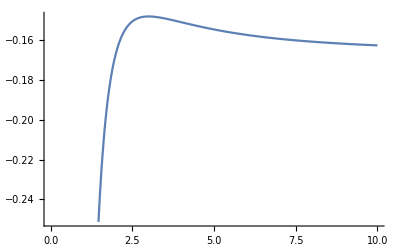

```mathematica
Plot[ Evaluate[ ( eq10  /. ϵ-> 0 /. M-> 1  /. L-> 1/. Λ-> 1  )],{r,0,10}]
```

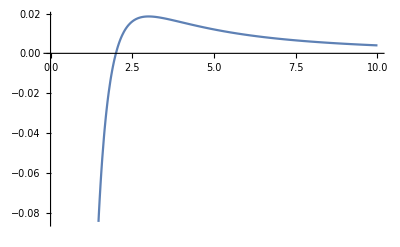

```mathematica
Plot[Evaluate[ ( eq10 /. ϵ-> 0/. M-> 1 /. L-> 1/. Λ-> 0 )], {r,0,10}]
```

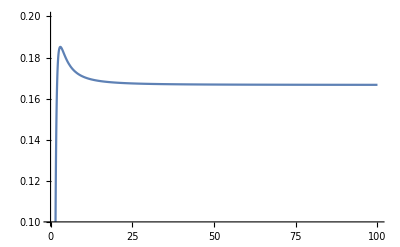

```mathematica
Plot[Evaluate[ ( eq10 /. ϵ-> 0/. M-> 1 /. L-> 1/. Λ-> -1)], {r,0,100}, PlotRange-> {0.1,0.2}]
```